```mathematica
dim=8;
Clear[μ,η]
A[6]=B[6]=μ
A[7]=B[7]=η
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

μ

η

```mathematica
(* Set up Initial values(SIC),Initial Step, RG steps, W, Z1, LnZ1, DLnZ1, and constants*)
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
```

```mathematica
SIC
Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
dA0dμ
Table[D[A[i]/.SAT,η],{i,0,dim-1}]
dA0dη
```

{B[0]→0,B[1]→η,B[2]→η,B[3]→μ,B[4]→1,B[5]→1}

{0,0,0,1,0,0,1,0}

{0,0,0,-4 μ,0,0,-4 μ,0}

{0,1,1,0,0,0,0,1}

{0,-2 η,-2 η,0,0,0,0,-2 η}

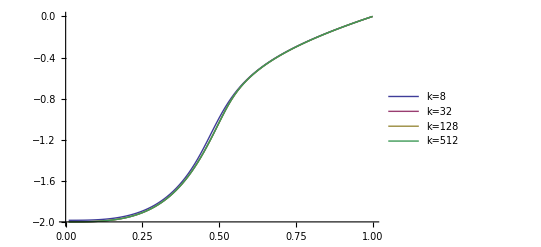

```mathematica
(***** Constants for IE: Internal Energy*****)
Clear[μ,η]
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
kVector={8,16,32,128,1024};
(******* Internal Energy <e> *******)
Clear[μ,η];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=1;
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
μind=0;
Do[
kind=1;
μind++;
InitRGW;
For[i=3,i≤Max[kVector],++i,
RGW;
If[i==kVector[[kind]],
Part[Part[IE,kind],μind]=-1.0/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT);kind++,];
],
{μ,μmin,μmax,μinc}
];
ListLinePlot[Table[Table[{μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=16","k=32","k=128","k=1024"},PlotStyle->Thick,AxesOrigin->{0,-2}]
```

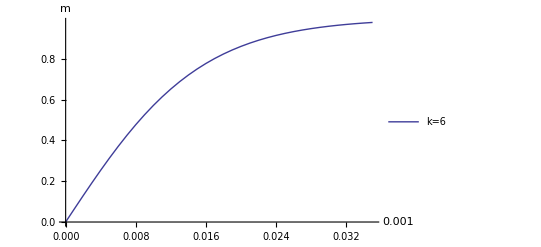

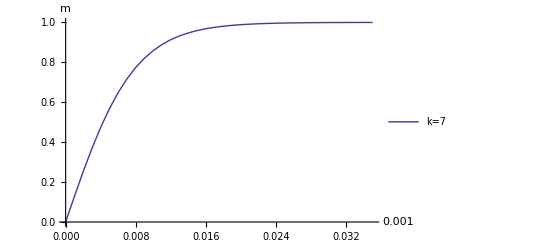

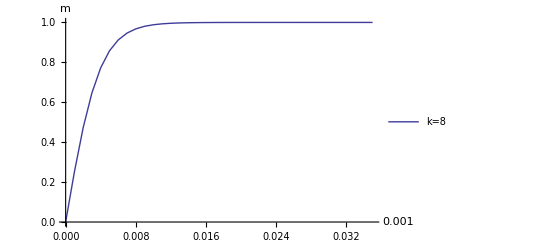

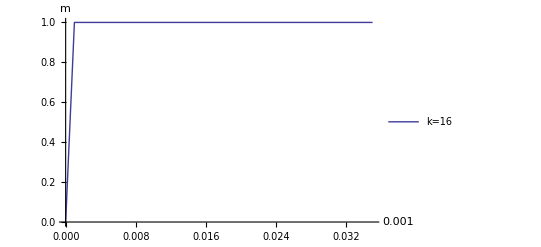

```mathematica
(***** Constants for magnetization: <m> vs H*****)
Clear[μ,η];
InitRGW;
Hmin=0.0;
Hmax=0.035;
Hinc=0.001;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-2*Hmin];
ηmin=Exp[-2*Hmax];
ηVector=Exp[-2*HVector];
kVector={6,7,8,16};
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
μ=0.01;
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^j+1.0)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[{HVector[[i]],Part[Part[MagH,1],i]},{i,1,Dimensions[HVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m} ]
ListLinePlot[Table[{HVector[[i]],Part[Part[MagH,2],i]},{i,1,Dimensions[HVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=7"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
ListLinePlot[Table[{HVector[[i]],Part[Part[MagH,3],i]},{i,1,Dimensions[HVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=8"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
ListLinePlot[Table[{HVector[[i]],Part[Part[MagH,4],i]},{i,1,Dimensions[HVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
```

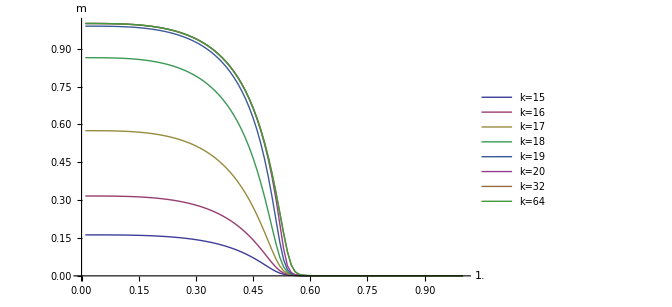

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={15,16,17, 18,19,20,32,64};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-0.00001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=15","k=16","k=17","k=18","k=19","k=20","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

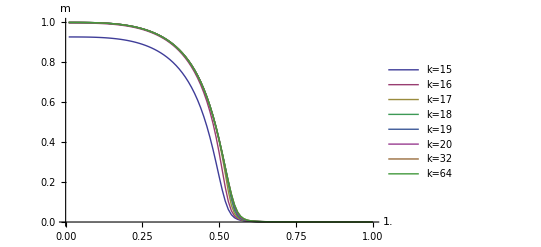

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={15,16,17, 18,19,20,32,64};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-0.0001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=15","k=16","k=17","k=18","k=19","k=20","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

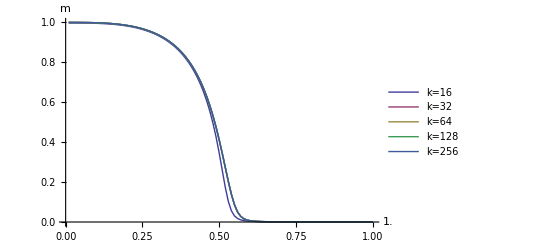

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={16,32,64,128,256};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-0.0001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

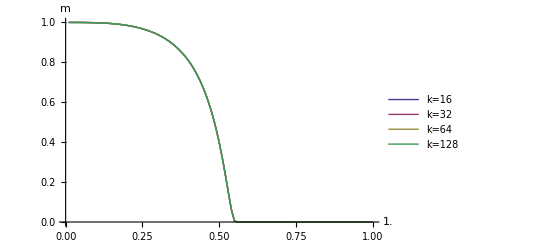

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.9999999999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

```mathematica
Exp[-0.000001]
```

0.999999

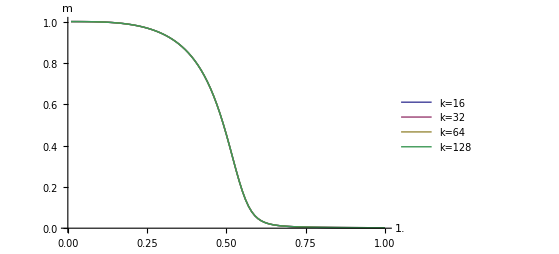

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

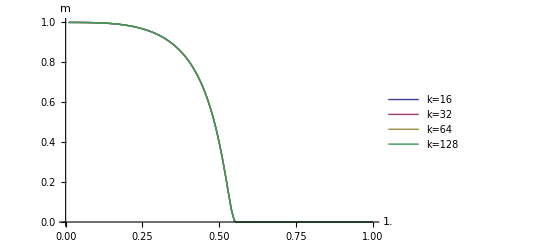

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.99999999999999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

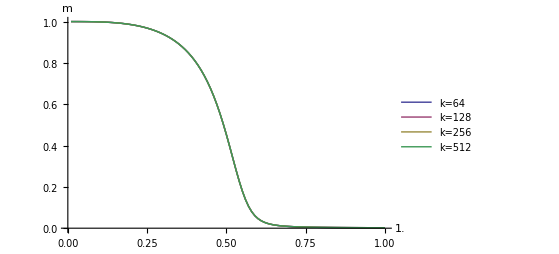
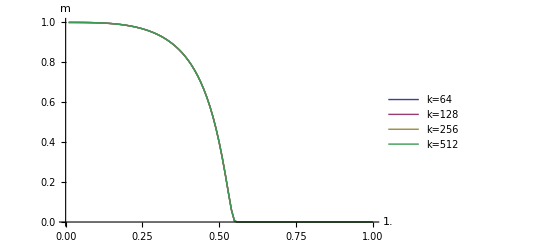
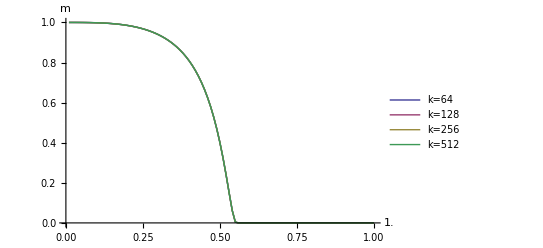
```mathematica
η=0.99999
-Graphics-

η=0.9999
-Graphics-

η=0.9999999999
-Graphics-

η=0.99999999999999
-Graphics-
```

```mathematica
Exp[-0.00001]
```

0.99999